```mathematica
SetOptions[Notebooks["NeelOverlap_v2.nb"]⟦1⟧,AutoGeneratedPackage->Automatic];
incr[digs_,base_]:=Module[{carry=1,ndigs=digs,k=1,nd},While[k≤Length[digs],{carry,nd}=QuotientRemainder[ndigs⟦k⟧+carry,base⟦k⟧];ndigs⟦k⟧=nd;If[carry==0,Break[]];k++;];ndigs];
t[i_,j_]:=2. Min[i,j]-1. KroneckerDelta[i,j];
UpB[L_,M_,α_,n_]:=(L-1.-∑_(j=1.)^M t[n,j] α⟦j⟧)/2.;
GenString[M_]:=Block[{part,part1,pair,d,j,k,m,p,check},m=M;part=Reap[While[m≠0,d=IntegerPart[RandomReal[{1.,M+1-1/10^12}]];j=IntegerPart[RandomReal[{1.,M+1-1/10^12}]];p=RandomReal[{0,1}];If[p≤(d PartitionsP[m-j d])/(m PartitionsP[m]),Sow[Table[d,{k,1,j}]];m=m-j d;];];];part1=Flatten[part];Table[Count[part1,i],{i,1,M}]];
ChooString[M_,L_,strOl_]:=Block[{string,mat,DDol,DDne,i,j,strNe,p,vec,vec1},string=strOl;mat=Table[t[i,j],{i,1,M},{j,1,M}];DDol=∏_(i=1)^M Binomial[L-Total[Table[mat⟦i,j⟧ string⟦j⟧,{j,1,M}]],string⟦i⟧];strNe=GenString[M];DDne=∏_(i=1)^M Binomial[L-Total[Table[mat⟦i,j⟧ strNe⟦j⟧,{j,1,M}]],strNe⟦i⟧];p=RandomReal[{0,1}];If[p≤Min[1,DDne/DDol],string=strNe;];string];
BTsel[M_,L_,α_]:=Block[{J,n,k},J=Table[RandomSample[Table[k,{k,-UpB[L,M,α,n],UpB[L,M,α,n]}],α⟦n⟧],{n,1,M}];J];
Theta[x_,m_,n_]:=If[n≠m,2 ArcTan[x/Abs[n-m]]+4 Sum[ArcTan[x/(Abs[n-m]+k)],{k,2,n+m-Abs[n-m]-2,2}]+2 ArcTan[x/(n+m)],4 Sum[ArcTan[x/k],{k,2,2 n-2,2}]+2 ArcTan[x/(2 n)]];
SolveBethe[M_,L_,string_,BN_]:=Block[{sol,x,n,g,b,m,o,h,check,sol1,bit,EE,EE1,EE2,EE3},check=1;bit=0;sol=Quiet[Table[ x[n][g],{n,1,M},{g,1,string⟦n⟧}]/.FindRoot[Flatten[Table[ArcTan[(x[n][g])/n]-(π BN⟦n,g⟧)/L-(∑_(m=1)^M ∑_(b=1)^string⟦m⟧ If[m≠n||b≠g,Theta[x[n][g]-x[m][b],m,n],0])/(2 L)==0,{n,1,M},{g,1,string⟦n⟧}]],Flatten[Table[{x[o][h],RandomReal[]},{o,1,M},{h,1,string⟦o⟧}],1],WorkingPrecision->15,MaxIterations->200,AccuracyGoal->15]];check=Flatten[Table[ArcTan[(sol⟦n⟧⟦g⟧)/n]-(π BN⟦n,g⟧)/L-(∑_(m=1)^M ∑_(b=1)^string⟦m⟧ If[m≠n||b≠g,Theta[sol⟦n⟧⟦g⟧-sol⟦m⟧⟦b⟧,m,n],0])/(2 L),{n,1,M},{g,1,string⟦n⟧}]];If[Total[Abs[check]]>1/10^11,Print["Findroot failed with string"];Print[BN];bit=1;];EE=If[M≠0,+Total[Flatten[Table[(2. n)/(sol⟦n,g⟧^2.+n^2.),{n,1,M},{g,1,string⟦n⟧}]]],-L/4];{bit,EE,BN,Chop[sol]}];
PIState[string_,BN_]:=Module[{BN1,BN2,i,check,tot},BN1=Table[Sort[-BN⟦i⟧],{i,1,Length[BN]}];BN2=Flatten[BN1];check=Select[BN2,Abs[#1]<1/10^13&];tot=Select[Flatten[BN],Abs[#1]>0&];If[BN==BN1&&check=={},0,1]];
NonZeroRap[rap_]:=Module[{rap1,check},rap1=Flatten[rap];check=Select[rap1,Abs[#1]<1/10^12&];If[check=={},0,1]];
Dtheta[x_,n_]:=(2 n)/(n^2+x^2);
DTheta[x_,m_,n_]:=If[n≠m,(2 Abs[m-n])/(x^2+Abs[m-n]^2)+4 Sum[(k+Abs[m-n])/(x^2+(k+Abs[m-n])^2),{k,2,n+m-Abs[n-m]-2,2}]+(2 (m+n))/((m+n)^2+x^2),4 Sum[k/(k^2+x^2),{k,2,2 n-2,2}]+(4 n)/(4 n^2+x^2)];
PP[x_,n_]:=Module[{k},If[OddQ[n],(x ∏_(k=0)^Floor[n/2] ((2 k+1)^2+x^2)/((2 k)^2+x^2))/(4^n √(n^2+x^2)),(√(n^2+x^2) ∏_(k=0)^(Floor[n/2]-1) ((2 k)^2+x^2)/((2 k+1)^2+x^2))/(4^n x)]];
CGm[i1_,j1_,i2_,j2_,string_,rap_]:=Module[{k,l},If[i1≠i2||j1≠j2,2 (DTheta[rap⟦i1,j1⟧-rap⟦i2,j2⟧,i1,i2]-DTheta[rap⟦i1,j1⟧+rap⟦i2,j2⟧,i1,i2]),2 (L-1) Dtheta[rap⟦i1,j1⟧,i1]-4 ∑_(k=1)^(i1-1) Dtheta[rap⟦i1,j1⟧,k]-2 ∑_(k=1)^Length[string] ∑_(l=1)^string⟦k⟧ If[i1≠k||j1≠l,DTheta[rap⟦i1,j1⟧-rap⟦k,l⟧,i1,k]+DTheta[rap⟦i1,j1⟧+rap⟦k,l⟧,i1,k],0]]];
CGp[i1_,j1_,i2_,j2_,string_,rap_]:=Module[{k,l},If[i1≠i2||j1≠j2,2 (DTheta[rap⟦i1,j1⟧-rap⟦i2,j2⟧,i1,i2]+DTheta[rap⟦i1,j1⟧+rap⟦i2,j2⟧,i1,i2]),2 L Dtheta[rap⟦i1,j1⟧,i1]-2 ∑_(k=1)^Length[string] ∑_(l=1)^string⟦k⟧ If[i1≠k||j1≠l,DTheta[rap⟦i1,j1⟧-rap⟦k,l⟧,i1,k]+DTheta[rap⟦i1,j1⟧+rap⟦k,l⟧,i1,k],0]]];
Overlap[string_,rap_,NI_]:=Module[{indx,ll,i,j,GGm,GGp},indx=Flatten[Table[Table[{i,j},{j,1,string⟦i⟧}],{i,1,Length[string]}],1];ll=Total[string];GGm=Table[CGm[indx⟦i,1⟧,indx⟦i,2⟧,indx⟦j,1⟧,indx⟦j,2⟧,string,rap],{i,1,ll},{j,1,ll}];GGp=Table[CGp[indx⟦i,1⟧,indx⟦i,2⟧,indx⟦j,1⟧,indx⟦j,2⟧,string,rap],{i,1,ll},{j,1,ll}];
(*Print[Det[GGp]];
Print[Det[GGm]];*)
((√2 NI! (∏_(i=1)^Length[string] ∏_(j=1)^string⟦i⟧ PP[rap⟦i,j⟧,i]) √(Det[GGp]/Det[GGm]))/(√((2 NI)!)))^2];
KK1[x_]:=2/(x^2+1);
KK12[x_]:=1/(x^2+1/4);
Kp[x_,y_]:=KK1[x-y]+KK1[x+y];
Km[x_,y_]:=KK1[x-y]-KK1[x+y];
Gp[j_,k_,rap_]:=KroneckerDelta[j,k] (L KK12[rap⟦j⟧]-∑_(p=1)^Length[rap] Kp[rap⟦j⟧,rap⟦p⟧])+Kp[rap⟦j⟧,rap⟦k⟧];
Gm[j_,k_,rap_]:=KroneckerDelta[j,k] (L KK12[rap⟦j⟧]-∑_(p=1)^Length[rap] Kp[rap⟦j⟧,rap⟦p⟧])+Km[rap⟦j⟧,rap⟦k⟧];
index[string_,k_]:=Module[{z,cont},cont=1;z=k;While[z>0,z=z-string⟦cont⟧;cont++;];cont-1];
OverlapAll[string_,rap1_,NI_]:=Module[{rap,rapstring,rpstr1,k,ll,i,j,GGm,GGp},rapstring={};rap=Flatten[rap1];For[k=1,k≤Length[rap],k++,AppendTo[rapstring,Table[rap⟦k⟧/2+((1+RandomReal[{10^-5,10^-6}]) ⅈ (index[string,k]+1-2 j))/2.,{j,1,index[string,k]}]];];rpstr1=Flatten[rapstring];ll=Length[rpstr1];GGp=Table[Gp[i,j,rpstr1],{i,1,ll},{j,1,ll}];GGm=Table[Gm[i,j,rpstr1],{i,1,ll},{j,1,ll}];
(*Print[Det[GGp]];
Print[Det[GGm]];*)
((√2 NI! (∏_(j=1)^ll (√(rpstr1⟦j⟧^2+1/4))/(4 rpstr1⟦j⟧)) √(Det[GGp]/Det[GGm]))/(√((2 NI)!)))^2];
L=8;
cont=0;
data=Reap[For[i=1,i≤L/2,i++,M=i;NI=L/2-i;base=Table[IntegerPart[M/j]+1,{j,1,M}];initial=Table[0,{k,1,M}];For[r=1,r≤∏_(b=1)^M base⟦b⟧,r++,If[∑_(s=1)^M s initial⟦s⟧==M,For[z=1,z≤M,z++,supp=Table[kk,{kk,0.5,UpB[L,M,initial,z]}];supp1=supp;PrependTo[supp1,-supp];supp2=Sort[Flatten[supp1]];
tab[z]=Subsets[supp2,{initial⟦z⟧}];
];
res=Table[tab[i],{i,1,M}];
res1=Tuples[res];
Print[{initial,res1}];
For[pp=1,pp≤Length[res1],pp++,If[PIState[initial,res1⟦pp⟧]==0,sol=SolveBethe[M,L,initial,res1⟦pp⟧];If[1>0,If[sol⟦1⟧==0,string=Table[1/2 Length[sol⟦3,k⟧],{k,1,Length[sol⟦3⟧]}];rap1=Table[Sort[sol⟦4,k⟧],{k,1,Length[sol⟦4⟧]}];rap=Table[Table[-rap1⟦k,j⟧,{j,1,string⟦k⟧}],{k,1,Length[sol⟦4⟧]}];
overlap=Overlap[string,rap,NI];Sow[{string,sol⟦2⟧,Flatten[sol⟦3⟧],Flatten[sol⟦4⟧],overlap}]];cont++;Print[cont];];];];Clear[tab];] (initial1=incr[initial,base]);initial=initial1;]]]⟦2⟧;
data1=Flatten[data,1];
Strconf=Table[data1⟦i,1⟧,{i,1,Length[data1]}];
BNumbers=Table[Flatten[data1⟦i,3⟧],{i,1,Length[data1]}];
Rapidities=Table[data1⟦i,4⟧,{i,1,Length[data1]}];
Obs=Table[{data1⟦i,2⟧,data1⟦i,5⟧},{i,1,Length[data1]}];
filename="/scratch/valba/Neel/Rap_L"<>ToString[L]<>".dat";
filename1="/scratch/valba/Neel/StrConf_L"<>ToString[L]<>".dat";
filename2="/scratch/valba/Neel/Bnum_L"<>ToString[L]<>".dat";
filename3="/scratch/valba/Neel/Obs_L"<>ToString[L]<>".dat";
(*Export[filename,Rapidities];
Export[filename1,Strconf];
Export[filename2,BNumbers];
Export[filename3,Obs];*)
```

{{1},{{{-2.5}},{{-1.5}},{{-0.5}},{{0.5}},{{1.5}},{{2.5}}}}

{{2,0},{{{-2.5,-1.5},{}},{{-2.5,-0.5},{}},{{-2.5,0.5},{}},{{-2.5,1.5},{}},{{-2.5,2.5},{}},{{-1.5,-0.5},{}},{{-1.5,0.5},{}},{{-1.5,1.5},{}},{{-1.5,2.5},{}},{{-0.5,0.5},{}},{{-0.5,1.5},{}},{{-0.5,2.5},{}},{{0.5,1.5},{}},{{0.5,2.5},{}},{{1.5,2.5},{}}}}

1

2

3

{{0,1},{{{},{-1.5}},{{},{-0.5}},{{},{0.5}},{{},{1.5}}}}

{{3,0,0},{{{-1.5,-0.5,0.5},{},{}},{{-1.5,-0.5,1.5},{},{}},{{-1.5,0.5,1.5},{},{}},{{-0.5,0.5,1.5},{},{}}}}

{{1,1,0},{{{-1.5},{-0.5},{}},{{-1.5},{0.5},{}},{{-0.5},{-0.5},{}},{{-0.5},{0.5},{}},{{0.5},{-0.5},{}},{{0.5},{0.5},{}},{{1.5},{-0.5},{}},{{1.5},{0.5},{}}}}

{{0,0,1},{{{},{},{-0.5}},{{},{},{0.5}}}}

{{4,0,0,0},{{{-1.5,-0.5,0.5,1.5},{},{},{}}}}

4

{{2,1,0,0},{}}

{{0,2,0,0},{{{},{-0.5,0.5},{},{}}}}

5

{{1,0,1,0},{}}

{{0,0,0,1},{}}

```mathematica
data1
```

{{{1,0},0.75302,{-2.5,2.5},{-2.07652139657234,2.07652139657234},0.02933128841618},{{1,0},2.44504,{-1.5,1.5},{-0.797473388882404,0.797473388882404},0.061248012581694},{{1,0},3.80194,{-0.5,0.5},{-0.22824347439015,0.228243474390149},0.4808492704307},{{2,0,0,0},5.65109,{-1.5,-0.5,0.5,1.5},{-1.05002420444733,-0.258945892749856,0.258945892749857,1.05002420444733},0.317280581708},{{0,1,0,0},1.63666,{-0.5,0.5},{-0.942343902894047,0.942343902894047},0.017253686195012}}

```mathematica
string={2,0,1,0};
rap={{-0.001,0.33515210869945453939108367357416738027`15.},{},{0.00001I},{}};
```

```mathematica
OverlapAll[string,rap,0]
```

-9.22115×10^6+2.25846×10^-9 ⅈ

```mathematica
Chop[Obs];
Sum[Obs[[i,1]] Obs[[i,2]],{i,1,Length[Obs]}]
```

9.71659

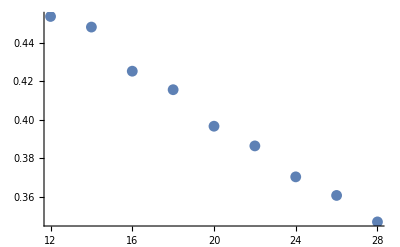

/u/he/valba/Dropbox/ETH/GGE/mathematica/test.dat

```mathematica
ener={{12,5.442962004927594},{14,6.273031793352902},{16,6.803029667635066},{18,7.480630144534813},{20,7.932998066031479},{22,8.501662188231945},{24,8.889187167849354},{26,9.379391750451337},{28,9.716594746897613}};
Table[{ener[[i,1]],ener[[i,2]]/ener[[i,1]]},{i,1,Length[ener]}]//ListPlot
Export["/u/he/valba/Dropbox/ETH/GGE/mathematica/test.dat",ener]
```

```mathematica
6.3402*0.05274+2.66666*0.0349596+5.203653*0.015022+3.7886939*0.0111444+2.44429*0.0058879+1.56067*0.00002698
```

0.562433

```mathematica
5.442962004927594+0.56243335256876
```

6.0054

```mathematica
data=Import["/scratch/valba/Neel/Obs_L32.dat"];
```

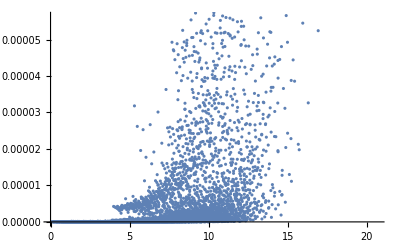

```mathematica
ListPlot[data]
```

```mathematica
Sum[data[[i,1]]*data[[i,2]] ,{i,1,Length[data]}]/32
```

0.325332

```mathematica
0.32533164051696756/0.6323334153953858
```

0.514494

```mathematica
1/32.
```

0.03125

```mathematica
L=32;
Q4[rap_,k_]:=2k(k^2-3rap^2)/(k^2+rap^2)^3;
StrConf=Import["/scratch/valba/Neel/StrConf_L32.dat"];
Rapid=Import["/scratch/valba/Neel/Rap_L32.dat"];
Obs=Import["/scratch/valba/Neel/Obs_L32.dat"];
StrGuide={};
For[i=1,i≤Length[StrConf],i++,
supp=Flatten[Table[Table[ j,{k,1,StrConf[[i,j]]}],{j,1,Length[StrConf[[i]]]}]];
AppendTo[supp,supp];
AppendTo[StrGuide,Flatten[supp]];
];
q4=Total[Table[Obs[[i,2]]Sum[Q4[Rapid[[i,j]],StrGuide[[i,j]]],{j,1,Length[Rapid[[i]]]}],{i,1,Length[Rapid]}]];
{L,q4/L,q4/L/Total[Obs][[2]]}
over=Total[Table[Obs[[i,2]],{i,1,Length[Rapid]}]];
ener=Total[Table[Obs[[i,2]]Obs[[i,1]],{i,1,Length[Rapid]}]];
{L,over}
{L,ener/L}
```

{32,0.141604,0.223939}

{32,0.632333}

{32,0.325332}

```mathematica
1/32.
```

0.03125

```mathematica
2^9
```

512

```mathematica
1/22.
```

0.0454545

```mathematica
final={{12,0.21544525558115782,0.24508250987484345},{14,0.21133200535378388,0.24458304993638233},{16,0.19645296583800395,0.23878965851944187},{18,0.19031297612932313,0.23726368787236488},{20,0.17931900123949443,0.23371091171042424},{24,0.16469520000820517,0.22961410184932096},{26,0.15927149860295414,0.22793719354281886},{28,0.15238922209433667,0.22635099242799725},{30,0.14769613551641703,0.22494164064176828},{32,0.14160384058739905,0.22393856965293707}};
Export["/u/he/valba/Dropbox/ETH/GGE/mathematica/q4.dat",final]
```

/u/he/valba/Dropbox/ETH/GGE/mathematica/q4.dat

```mathematica
-Δ/2 D[(1-Δ^2)/(Cosh[√(1-Δ^2)x]-Δ^2),{x,2}]/.{x->0}
```

Δ/2

```mathematica
1/2 Δ (6/1)
```

```mathematica
(Binomial[10,5]/2+512)
```

638